# Droplet size by BM analysis

## Radius by pressure

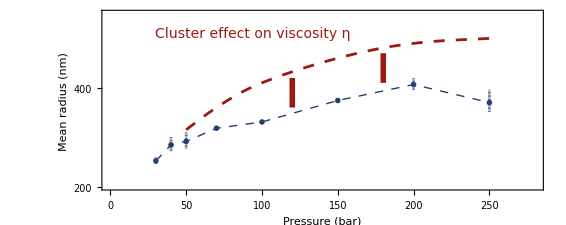

```mathematica
(* -- import -- *)
dt=Import[NotebookDirectory[]<>"data/radius.mx"];
dtCorrection={{50,290},{70,350},{100,400},{150,450},{200,480},{250,490}};

(* -- plot -- *)
gfBase=ListLinePlot[

dt,

Epilog->{
(* -- panel label -- *)
Text[Style["a",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
(* -- viscosity effect -- *)
{RGBColor[.60,.11,.07],AbsoluteThickness[4],{Arrowheads[.03],Arrow[{{120,360},{120,420}}]}},
{RGBColor[.60,.11,.07],AbsoluteThickness[4],{Arrowheads[.03],Arrow[{{180,410},{180,470}}]}},
Text[Style["Cluster effect on viscosity η",FontColor->RGBColor[.60,.11,.07],FontSize->14,FontWeight->Plain],Scaled@{.12,.91},{-1,1}]
},

Joined->True,
PlotRange->{{0,280},{200,550}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},

PlotStyle->{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[1],AbsoluteDashing[6]},

PlotMarkers->Graphics[{EdgeForm[{RGBColor[.14,.25,.44,1],AbsoluteThickness[2]}],FaceForm[{RGBColor[.54,.62,.72,1]}],Disk[{0,0},Offset[4]]}],

IntervalMarkers->"Bars",
IntervalMarkersStyle->{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[2],AbsoluteDashing[0]},

Frame->True,
FrameTicks->{
Table[{{i,i,{.015,0}},{i,Null,{.015,0}}},{i,0,500,100}]ᵀ,{Table[{i,If[Mod[i,50]==0,i,Null],{If[Mod[i,50]==0,.015,.008],0}},{i,0,300,25}],
Table[{i,Null,{If[Mod[i,50]==0,.015,.008],0}},{i,0,300,25}]}
},
FrameLabel->{{"Mean radius (nm)",None},{"Pressure (bar)",None}},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

GridLines->None,

ImagePadding->{{50,10},{45,10}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->0.4

];

(* -- correction -- *)
dtCorrection={{50,315},{70,360},{100,410},{150,460},{200,490},{250,500}};
gfCorr=ListLinePlot[
dtCorrection,
InterpolationOrder->2,
PlotStyle->{{RGBColor[.60,.11,.07],Opacity[1],AbsoluteThickness[2],AbsoluteDashing[8]}}
];

(* -- show plot -- *)
gfa=Show[{gfBase,gfCorr}];
Print[gfa];
```

## 100 bar

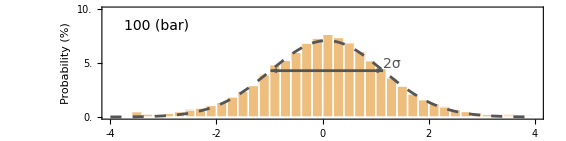

```mathematica
(* -- function 1: Gaussian fit for time sectional data -- *)
gaussFit[dx_]:=Block[{bins,counts,centers,model,nlm},
{bins,counts}=HistogramList[dx,{.2},"Probability"];
centers=MovingAverage[bins,2];
Clear[a,b,x];
model=a Exp[-(x-b)^2/c/2];
nlm=NonlinearModelFit[{centers,counts}ᵀ,model,{{a,.1},b,{c,1}},x];
Return[nlm];
];

(* -- function 2: droplet size -- *)
radius[var_,pressure_]:=Block[{Δt,η,kT,r},
Δt=1/50;
η=<|30->2.2961,40->2.3231,50->2.3522,70->2.4168,100->2.5296,150->2.7582,200->3.0293,250->3.3295|>*10^-5; (* [Pa·s] *)
kT=294*1.38*^-23; (* [J] *)
r=10^18 (2Δt) kT/(6π η[pressure] var); (* [μm] *)
Return[r];
];

(* -- import -- *)
p=100;
dx=Import[NotebookDirectory[]<>"data/"<>ToString[p]<>".mx"];

(* -- calulation -- *)
nlm=gaussFit[dx];
var=Flatten[{Values@nlm["BestFitParameters"][[3]],
nlm["ParameterConfidenceIntervals",ConfidenceLevel->.99][[3]]}];
rList=radius[var,p];
r=rList[[1]];

stdPoints={{b-√(Abs@c),a Exp[-1/2]},{b+√(Abs@c),a Exp[-1/2]}}/.nlm["BestFitParameters"];

(* -- plot -- *)
lb=ToString@p<>" (bar)";

gfb1=Histogram[

Select[dx,Between[{-4,4}]],{.2},"Probability",

PlotRange->{{-4,4},{0,.1}},
PlotRangePadding->0,
PlotRangeClipping->False,

Epilog->{
(* -- panel label -- *)
Text[Style["b",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
(* -- pressure --*)
Text[Style[lb,FontColor->Black,FontSize->14,FontWeight->Plain],Scaled[{.05,.9}],{-1,1}]
},

ChartBaseStyle->EdgeForm[{White,Opacity[1],AbsoluteThickness[1]}],
ChartStyle->{Directive[RGBColor[.91,.64,.28],Opacity[.7]]},

LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},

Axes->False,

Frame->True,
FrameTicks->{
{Table[{i/100,i,{.015,0}},{i,0,10,2.5}],
Table[{i/100,Null,{.015,0}},{i,0,10,2.5}]},
Table[{{i,i,{.02,0}},{i,Null,{.02,0}}},{i,-4,4,2}]ᵀ
},
FrameLabel->{{"Probability (%)",None},{"Displacement (μm)",None}},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

GridLines->None,

ImagePadding->{{50,10},{45,10}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->0.25

];

gfb2=Plot[nlm[x],{x,-4,4},PlotStyle->{Darker@Gray,Opacity[1],AbsoluteDashing[8],AbsoluteThickness[2]}];

gfb3=Graphics[{
{Darker@Gray,AbsoluteThickness[2],Arrowheads[{-.03,.03}],Arrow[stdPoints]},
Text[Style["2σ",FontColor->Darker@Gray,FontSize->14,FontWeight->Plain],stdPoints[[2]],{-1.5,-1}]
}];

gfb=Show[{gfb1,gfb2,gfb3}];
Print[gfb];
```

## 250 bar

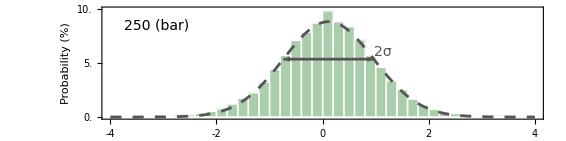

```mathematica
(* -- function 1: Gaussian fit for time sectional data -- *)
gaussFit[dx_]:=Block[{bins,counts,centers,model,nlm},
{bins,counts}=HistogramList[dx,{.2},"Probability"];
centers=MovingAverage[bins,2];
Clear[a,b,x];
model=a Exp[-(x-b)^2/c/2];
nlm=NonlinearModelFit[{centers,counts}ᵀ,model,{{a,.1},b,{c,1}},x];
Return[nlm];
];

(* -- function 2: droplet size -- *)
radius[var_,pressure_]:=Block[{Δt,η,kT,r},
Δt=1/50;
η=<|30->2.2961,40->2.3231,50->2.3522,70->2.4168,100->2.5296,150->2.7582,200->3.0293,250->3.3295|>*10^-5; (* [Pa·s] *)
kT=294*1.38*^-23; (* [J] *)
r=10^18 (2Δt) kT/(6π η[pressure] var); (* [μm] *)
Return[r];
];

(* -- import -- *)
p=250;
dx=Import[NotebookDirectory[]<>"data/"<>ToString[p]<>".mx"];

(* -- calulation -- *)
nlm=gaussFit[dx];
var=Flatten[{Values@nlm["BestFitParameters"][[3]],
nlm["ParameterConfidenceIntervals",ConfidenceLevel->.99][[3]]}];
rList=radius[var,p];
r=rList[[1]];

stdPoints={{b-√(Abs@c),a Exp[-1/2]},{b+√(Abs@c),a Exp[-1/2]}}/.nlm["BestFitParameters"];

(* -- plot -- *)
lb=ToString@p<>" (bar)";

gfc1=Histogram[

Select[dx,Between[{-4,4}]],{.2},"Probability",

PlotRange->{{-4,4},{0,.1}},
PlotRangePadding->0,
PlotRangeClipping->False,

Epilog->{
(* -- panel label -- *)
Text[Style["c",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
(* -- pressure --*)
Text[Style[lb,FontColor->Black,FontSize->14,FontWeight->Plain],Scaled[{.05,.9}],{-1,1}]
},

ChartBaseStyle->EdgeForm[{White,Opacity[1],AbsoluteThickness[1]}],
ChartStyle->{Directive[RGBColor[.53,.73,.53],Opacity[.7]]},

LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},

Axes->False,

Frame->True,
FrameTicks->{
{Table[{i/100,i,{.015,0}},{i,0,10,2.5}],
Table[{i/100,Null,{.015,0}},{i,0,10,2.5}]},
Table[{{i,i,{.02,0}},{i,Null,{.02,0}}},{i,-4,4,2}]ᵀ
},
FrameLabel->{{"Probability (%)",None},{"Displacement (μm)",None}},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

GridLines->None,

ImagePadding->{{50,10},{45,10}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->0.25

];

gfc2=Plot[nlm[x],{x,-4,4},PlotStyle->{Darker@Gray,Opacity[1],AbsoluteDashing[8],AbsoluteThickness[2]}];

gfc3=Graphics[{
{Darker@Gray,AbsoluteThickness[2],Arrowheads[{-.03,.03}],Arrow[stdPoints]},
Text[Style["2σ",FontColor->Darker@Gray,FontSize->14,FontWeight->Plain],stdPoints[[2]],{-1.5,-1}]
}];

gfc=Show[{gfc1,gfc2,gfc3}];
Print[gfc];
```

## Merge figures

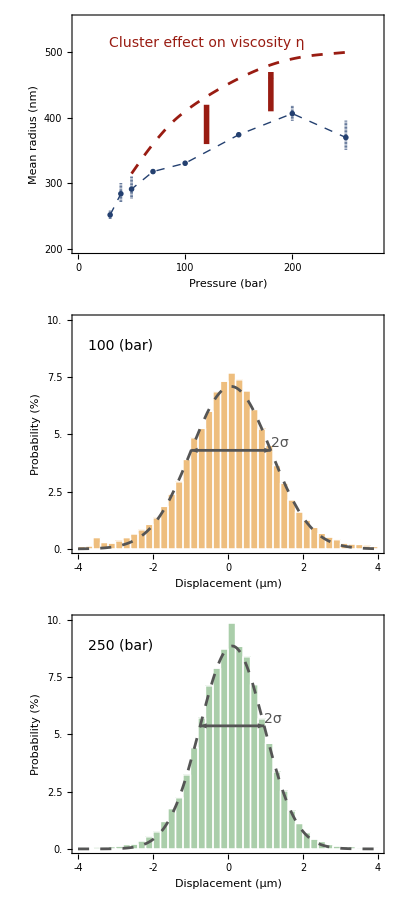

```mathematica
gf=Grid[{{gfa},{gfb},{gfc}},Spacings->0];
Print[gf];

Export[NotebookDirectory[]<>"size.pdf",gf];
```

# Displacement distribution by size distribution

## Forward modeling of Brownian motion analysis

## Data

```mathematica
(* -- functions -- *)
normalDistribution[r0_,σr_]:=
N@Table[
{r,PDF[NormalDistribution[r0,σr],r]},
{r,Max[r0-5σr,.1],r0+5σr,σr/10}
];

doubleGaussian[r1_,r2_,σr1_,σr2_]:=
N@Table[
{r,(PDF[NormalDistribution[r1,σr1],r]+PDF[NormalDistribution[r2,σr2],r])/2},
{r,Max[r1-5σr1,.1],r2+5σr2,Min[σr1,σr2]/10}
];

displacementDistribution[sizeDistribution_]:=Block[{σ,xRange,dt,raw},
σ[r0_]:=√((2*294*1.38*^-23/50)/(6π 2.5296*^-5*r0*10^-9))*10^6;
xRange=Range[-6,6,.05];
raw=ParallelTable[
Total@MapThread[#2*PDF[NormalDistribution[0,σ[#1]],x]&,sizeDistributionᵀ]
,{x,xRange}];
dt={xRange,raw/Max[raw]}ᵀ;
Return[dt];
];

σGaussFit[dt_]:=Block[{nlm,σx},
nlm=NonlinearModelFit[dt,Exp[-(1/2)x^2/a],a,x];
σx=Values@nlm["BestFitParameters"][[1]];
Return[SetPrecision[σx,3]];
];

statistics[sizeDistribution_]:=Block[{r,dr,prob,mr,σr},
r=MovingAverage[sizeDistributionᵀ[[1]],2];
dr=Differences[sizeDistributionᵀ[[1]]];
prob=MovingAverage[sizeDistributionᵀ[[2]],2];
mr=Total@(r*dr*prob); (* mean *)
σr=Sqrt@Total@((r-mr)^2*dr*prob); (* standard deviation *)
Return[SetPrecision[{mr,σr},3]];
];

(* -- calculation -- *)
f=<|
"f1"->normalDistribution[150,30],
"f2"->normalDistribution[300,30],
"f3"->normalDistribution[300,55],
"f4"->doubleGaussian[250,350,10,30]
|>;
{mr,σr}=(statistics/@Values[f])ᵀ;

dt=displacementDistribution/@Values[f];
σx=σGaussFit/@dt;

(* -- display -- *)
lb={mr,σr,σx};
Style[TableForm[lb,TableHeadings->{{"m_r","σ_r","σ_x"},Keys[f]}],FontSize->15]//Print;
```

| f1 | f2 | f3 | f4
m_r | 150. | 300. | 300. | 300.
σ_r | 30. | 30. | 55.1 | 54.8
σ_x | 2.28 | 1.14 | 1.14 | 1.14

## Plot

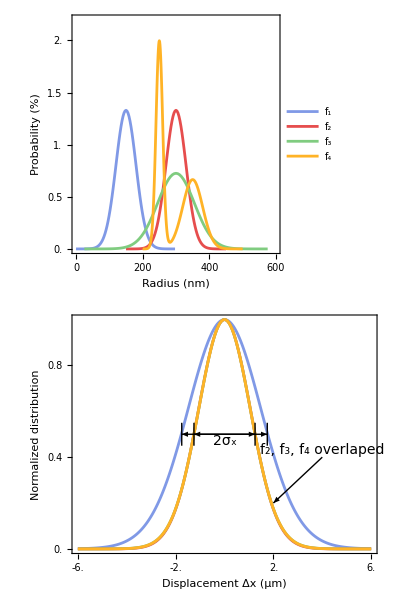

```mathematica
(* -- 2σ points -- *)
pts=Table[
sel=dt[[i,All,2]];
idx=Flatten[Position[sel,_?(#≥Max[sel]/2&)]][[{1,-1}]];
{dt[[i,idx,1]],{.5,.5}}ᵀ,
{i,2}];

(* -- plot style -- *)
clr={RGBColor[.5,.6,.9],RGBColor[.9,.3,.3],RGBColor[.5,.8,.5],RGBColor[1,.7,.15]};
ps={#,AbsoluteThickness[2]}&/@clr;

(* -- plot -- *)
gfa=ListLinePlot[

f,

Epilog->{Text[Style["a",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}]},

PlotRange->{{0,600},{0,.022}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},

PlotStyle->ps,

PlotLegends->Placed[
LineLegend[
{"f_1","f_2","f_3","f_4"},
LegendMarkerSize->{{30,10}},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMargins->1,LegendLayout->"Column"],
{Scaled@({.92,.92}),{1,1}}],

Axes->False,
Frame->True,
FrameTicks->{
{Table[{i/100,If[Mod[i,.5]==0,i,Null],{If[Mod[i,.5]==0,.015,.008],0}},{i,0,2.5,.1}],
Table[{i/100,Null,{If[Mod[i,.5]==0,.015,.008],0}},{i,0,2.5,.1}]},
{Table[{i,If[Mod[i,100]==0,i,Null],{If[Mod[i,100]==0,.015,.008],0}},{i,0,600,20}],
Table[{i,Null,{If[Mod[i,100]==0,.015,.008],0}},{i,0,600,20}]}
},
FrameLabel->{"Radius (nm)","Probability (%)"},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

GridLines->None,

ImagePadding->{{45,15},{45,10}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->.5

];

gfb=ListLinePlot[

dt,

Epilog->{
Text[Style["b",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
Table[{Black,AbsoluteThickness[1],Line[{pts[[i,j]]+{0,.05},pts[[i,j]]-{0,.05}}]},{i,2},{j,2}],
{Black,AbsoluteThickness[1],Arrowheads[{-.02,.02}],Arrow[pts[[1]]]},
{Black,AbsoluteThickness[1],Arrowheads[{-.02,.02}],Arrow[pts[[2]]]},
Text[Style["2σ_x",{FontColor->Black,FontSize->14,FontWeight->Plain}],{0,.5},{0,1}],
{Black,AbsoluteThickness[1],Arrowheads[{0,.02}],Arrow[{{4,.4},{2,.2}}]},
Text[Style[StringForm["`1`, `2`, `3` overlaped",Style["f_2",clr[[2]]],Style["f_3",clr[[3]]],Style["f_4",clr[[4]]]],{FontColor->Black,FontSize->14,FontWeight->Plain}],{4,.4},{0,-1}]
},

PlotRange->{{-6,6},{0,1}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},

PlotStyle->ps,

Axes->False,
Frame->True,
FrameTicks->{
{Table[{i/10,If[Mod[i,2]==0,N@(i/10),Null],{If[Mod[i,2]==0,.015,.008],0}},{i,0,20,1}],
Table[{i/10,Null,{If[Mod[i,2]==0,.015,.008],0}},{i,0,20,1}]},
{Table[{i,If[Mod[i,2]==0,i,Null],{If[Mod[i,2]==0,.015,.008],0}},{i,-6,6,.5}],
Table[{i,Null,{If[Mod[i,2]==0,.015,.008],0}},{i,-6,6,.5}]}
},
FrameLabel->{"Displacement Δx (μm)","Normalized distribution"},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

GridLines->None,

ImagePadding->{{45,15},{45,10}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->.5

];


gf=Grid[{{gfa},{gfb}},Spacings->0];
Print[gf];

Export[NotebookDirectory[]<>"distributionEffect.pdf",gf];
```